```mathematica
triangelNumber[n_]:=(n(n+1))/2;
squareNumber[n_]:=n^2;
pentagonalNumber[n_]:=(n(3n-1))/2;
hexagonalNumber[n_]:=n(2n-1);
heptagonalNumber[n_]:=(n(5n-3))/2;
octagonalNumber[n_]:=n(3n-2);
head[n_,i_]:=(n-Mod[n,10^i])/10^i;
tail[n_,i_]:=Mod[n,10^i];
```

```mathematica
cyclic[a_,b_]:=tail[a,2]==head[b,2];
```

```mathematica
triangelNumber[45]
triangelNumber[140]
```

1035

9870

```mathematica
squareNumber[32]
squareNumber[99]
```

1024

9801

```mathematica
pentagonalNumber[26]
pentagonalNumber[81]
```

1001

9801

```mathematica
hexagonalNumber[23]
hexagonalNumber[70]
```

1035

9730

```mathematica
heptagonalNumber[21]
heptagonalNumber[63]
```

1071

9828

```mathematica
octagonalNumber[19]
octagonalNumber[58]
```

1045

9976

```mathematica
f3s=Table[triangelNumber[n],{n,45,140}]
```

{1035,1081,1128,1176,1225,1275,1326,1378,1431,1485,1540,1596,1653,1711,1770,1830,1891,1953,2016,2080,2145,2211,2278,2346,2415,2485,2556,2628,2701,2775,2850,2926,3003,3081,3160,3240,3321,3403,3486,3570,3655,3741,3828,3916,4005,4095,4186,4278,4371,4465,4560,4656,4753,4851,4950,5050,5151,5253,5356,5460,5565,5671,5778,5886,5995,6105,6216,6328,6441,6555,6670,6786,6903,7021,7140,7260,7381,7503,7626,7750,7875,8001,8128,8256,8385,8515,8646,8778,8911,9045,9180,9316,9453,9591,9730,9870}

```mathematica
f4s=Table[squareNumber[n],{n,32,99}]
```

{1024,1089,1156,1225,1296,1369,1444,1521,1600,1681,1764,1849,1936,2025,2116,2209,2304,2401,2500,2601,2704,2809,2916,3025,3136,3249,3364,3481,3600,3721,3844,3969,4096,4225,4356,4489,4624,4761,4900,5041,5184,5329,5476,5625,5776,5929,6084,6241,6400,6561,6724,6889,7056,7225,7396,7569,7744,7921,8100,8281,8464,8649,8836,9025,9216,9409,9604,9801}

```mathematica
f5s=Table[pentagonalNumber[n],{n,26,81}]
```

{1001,1080,1162,1247,1335,1426,1520,1617,1717,1820,1926,2035,2147,2262,2380,2501,2625,2752,2882,3015,3151,3290,3432,3577,3725,3876,4030,4187,4347,4510,4676,4845,5017,5192,5370,5551,5735,5922,6112,6305,6501,6700,6902,7107,7315,7526,7740,7957,8177,8400,8626,8855,9087,9322,9560,9801}

```mathematica
f6s=Table[hexagonalNumber[n],{n,23,70}]
```

{1035,1128,1225,1326,1431,1540,1653,1770,1891,2016,2145,2278,2415,2556,2701,2850,3003,3160,3321,3486,3655,3828,4005,4186,4371,4560,4753,4950,5151,5356,5565,5778,5995,6216,6441,6670,6903,7140,7381,7626,7875,8128,8385,8646,8911,9180,9453,9730}

```mathematica
f7s=Table[heptagonalNumber[n],{n,21,63}]
```

{1071,1177,1288,1404,1525,1651,1782,1918,2059,2205,2356,2512,2673,2839,3010,3186,3367,3553,3744,3940,4141,4347,4558,4774,4995,5221,5452,5688,5929,6175,6426,6682,6943,7209,7480,7756,8037,8323,8614,8910,9211,9517,9828}

```mathematica
f8s=Table[octagonalNumber[n],{n,19,58}]
```

{1045,1160,1281,1408,1541,1680,1825,1976,2133,2296,2465,2640,2821,3008,3201,3400,3605,3816,4033,4256,4485,4720,4961,5208,5461,5720,5985,6256,6533,6816,7105,7400,7701,8008,8321,8640,8965,9296,9633,9976}

```mathematica
6! Length[f8s]
```

28800

```mathematica
Length[f3s] Length[f4s] Length[f5s] Length[f6s] Length[f7s] Length[f8s]
```

30181294080

```mathematica
Select
```

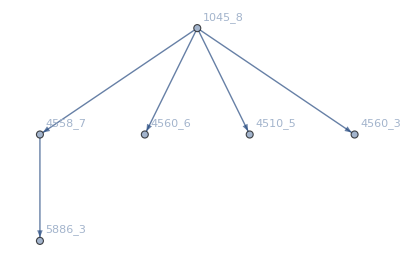

```mathematica
Graph[{
"1045_8"-> "4558_7",
"1045_8"-> "4560_6",
"1045_8"-> "4510_5",
"1045_8"-> "4560_3",
"4558_7"-> "5886_3"
},VertexLabels->"Name"]
```

```mathematica
5^5
```

3125